```mathematica
P(s|m)= (P(m|s)P(s))/(P(m))
```

```mathematica
1/(Gamma[r]/(r!))Exp[-λ] λ^r/(r!)1/λ
```

```mathematica
post=(ⅇ^-λ λ^(-1+r))/Gamma[r]
```

(ⅇ^-λ λ^(-1+r))/Gamma[r]

```mathematica
∫_0^∞ Exp[-λ] λ^r/(r!)1/λ ⅆλ
```

ConditionalExpression[Gamma[r]/(r!),Re[r]>0]

```mathematica
Solve[D[(ⅇ^-λ λ^(-1+r))/Gamma[r],λ]==0,λ]
```

{{λ→-1+r}}

```mathematica
(ⅇ^-λ λ^(-1+r))/Gamma[r]/.{λ->-1+r}//Simplify
```

```mathematica
(ⅇ^(1-r) (-1+r)^(-1+r))/((r-1)!)//Simplify
```

```mathematica
L=Log[(ⅇ^-λ λ^(-1+r))/Gamma[r]]
```

Log[(ⅇ^-λ λ^(-1+r))/Gamma[r]]

```mathematica
D[D[L,λ],λ]//Simplify
```

(1-r)/λ^2

```mathematica
c=1/(r-1)
```

1/(-1+r)

```mathematica
PolyGamma
```

```mathematica
1/((-1+r) ((-1+r)!)^2)(((-1+r)!)^2+(-1+r) Gamma[r]^2 PolyGamma[0,r]^2-(-1+r) (-1+r)! Gamma[r] (PolyGamma[0,r]^2+PolyGamma[1,r]))
```

```mathematica
Gamma[4]
```

6

```mathematica
PolyGamma[1,3]
```

-5/4+π^2/6

```mathematica
c
```

1/9

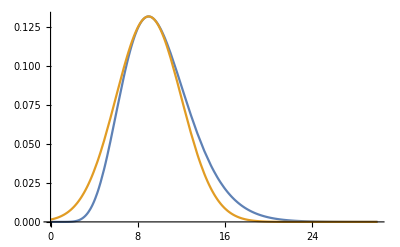

```mathematica
c=1/(r-1);r=10;Plot[{Exp[-λ] λ^r/(r!)1/λ r,(ⅇ^(1-r) (-1+r)^(-1+r))/((r-1)!)Exp[-c/2(λ-(r-1))^2]},{λ,0,30}]
```

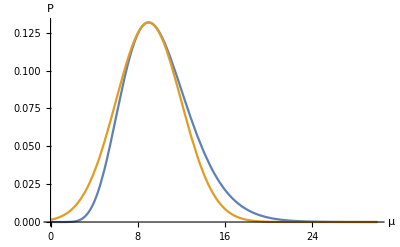

```mathematica
Show[%2,AxesLabel->{HoldForm[μ],HoldForm[P]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

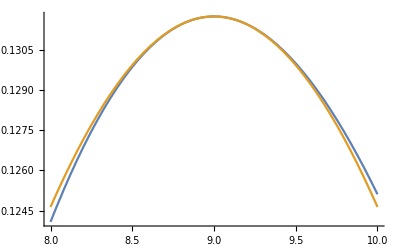

```mathematica
r=10;Plot[{Exp[-λ] λ^r/(r!)1/λ r,(ⅇ^(1-r) (-1+r)^(-1+r))/((r-1)!)Exp[-c/2(λ-(r-1))^2]},{λ,8,10}]
```

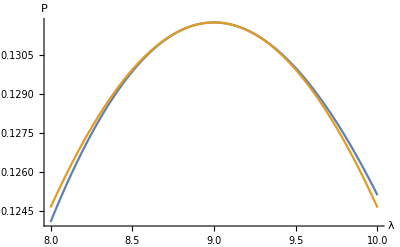

```mathematica
Show[%39,AxesLabel->{HoldForm[λ],HoldForm[P]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Clear[r]
```

```mathematica
{Exp[-λ] λ^r/(r!)r}/.λ->Exp[x]
```

{(ⅇ^(-ⅇ^x) (ⅇ^x)^r r)/(r!)}

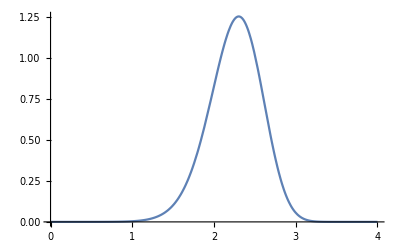

```mathematica
r=10;Plot[(ⅇ^(-ⅇ^x) (ⅇ^x)^r r)/(r!),{x,0,4}]
```